# Finding fixed points and the best responses graph of 2p2a games.

```mathematica
(*Check if the best player 2 uses the best strategy against player 1 and vice versa.*)
result[i_]:=
Module[{input = i},
(*Make assumptions on the Q-values and the game, based on the strategy.*)
assumptions = {
               If[input[[1]]==0, Q1000>Q1001, Q1000<Q1001],
               If[input[[2]]==0, Q1010>Q1011, Q1010<Q1011],
               If[input[[3]]==0, Q1100>Q1101, Q1100<Q1101],
               If[input[[4]]==0, Q1110>Q1111, Q1110<Q1111],
               If[input[[5]]==0, Q2000>Q2001, Q2000<Q2001],
               If[input[[6]]==0, Q2010>Q2011, Q2010<Q2011],
               If[input[[7]]==0, Q2100>Q2101, Q2100<Q2101],
               If[input[[8]]==0, Q2110>Q2111, Q2110<Q2111],
               r>t>p>s,0<d<1};

(*Make the Bellman equations.*)
Assuming[assumptions,
{
q1 = Simplify[Boole[Q2000>Q2001] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2000<Q2001] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q2=  Simplify[Boole[Q2000>Q2001] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2000<Q2001] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q3=  Simplify[Boole[Q2100>Q2101] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2100<Q2101] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q4=  Simplify[Boole[Q2100>Q2101] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2100<Q2101] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q5=  Simplify[Boole[Q2010>Q2011] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2010<Q2011] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q6=  Simplify[Boole[Q2010>Q2011] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2010<Q2011] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q7=  Simplify[Boole[Q2110>Q2111] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                         Boole[Q2110<Q2111] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q8=  Simplify[Boole[Q2110>Q2111] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                         Boole[Q2110<Q2111] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q9=  Simplify[Boole[Q1000>Q1001] (p+d*Q2000*Boole[Q2000>Q2001]+d*Q2001*Boole[Q2000<Q2001])+
                         Boole[Q1000<Q1001] (t+d*Q2010*Boole[Q2010>Q2011]+d*Q2011*Boole[Q2010<Q2011])],q10=Simplify[Boole[Q1000>Q1001] (s+d*Q2100*Boole[Q2100>Q2101]+d*Q2101*Boole[Q2100<Q2101])+
                         Boole[Q1000<Q1001] (r+d*Q2110*Boole[Q2110>Q2111]+d*Q2111*Boole[Q2110<Q2111])],q11=Simplify[Boole[Q1100>Q1101] (p+d*Q2000*Boole[Q2000>Q2001]+d*Q2001*Boole[Q2000<Q2001])+        
                         Boole[Q1100<Q1101] (t+d*Q2010*Boole[Q2010>Q2011]+d*Q2011*Boole[Q2010<Q2011])],q12=Simplify[Boole[Q1100>Q1101] (s+d*Q2100*Boole[Q2100>Q2101]+d*Q2101*Boole[Q2100<Q2101])+
                         Boole[Q1100<Q1101] (r+d*Q2110*Boole[Q2110>Q2111]+d*Q2111*Boole[Q2110<Q2111])],q13=Simplify[Boole[Q1010>Q1011] (p+d*Q2000*Boole[Q2000>Q2001]+d*Q2001*Boole[Q2000<Q2001])+
                         Boole[Q1010<Q1011] (t+d*Q2010*Boole[Q2010>Q2011]+d*Q2011*Boole[Q2010<Q2011])],q14=Simplify[Boole[Q1010>Q1011] (s+d*Q2100*Boole[Q2100>Q2101]+d*Q2101*Boole[Q2100<Q2101])+
                         Boole[Q1010<Q1011] (r+d*Q2110*Boole[Q2110>Q2111]+d*Q2111*Boole[Q2110<Q2111])],q15=Simplify[Boole[Q1110>Q1111] (p+d*Q2000*Boole[Q2000>Q2001]+d*Q2001*Boole[Q2000<Q2001])+
                         Boole[Q1110<Q1111] (t+d*Q2010*Boole[Q2010>Q2011]+d*Q2011*Boole[Q2010<Q2011])],q16=Simplify[Boole[Q1110>Q1111] (s+d*Q2100*Boole[Q2100>Q2101]+d*Q2101*Boole[Q2100<Q2101])+               
                         Boole[Q1110<Q1111] (r+d*Q2110*Boole[Q2110>Q2111]+d*Q2111*Boole[Q2110<Q2111])]
}];

sol1=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111},{Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111}];
formula1 = Assuming[assumptions,
 Simplify[Reduce[
  If[input[[1]]==0,Simplify[sol1[[1]][[1]][[2]] > sol1[[1]][[2]][[2]]], Simplify[sol1[[1]][[1]][[2]] < sol1[[1]][[2]][[2]]]] && 
If[input[[2]]==0,Simplify[sol1[[1]][[3]][[2]] > sol1[[1]][[4]][[2]]], Simplify[sol1[[1]][[3]][[2]] < sol1[[1]][[4]][[2]]]] && 
If[input[[3]]==0,Simplify[sol1[[1]][[5]][[2]] > sol1[[1]][[6]][[2]]], Simplify[sol1[[1]][[5]][[2]] < sol1[[1]][[6]][[2]]]] && 
If[input[[4]]==0,Simplify[sol1[[1]][[7]][[2]] > sol1[[1]][[8]][[2]]], Simplify[sol1[[1]][[7]][[2]] < sol1[[1]][[8]][[2]]]],d,Reals]]];

sol2=Solve[{q9==Q2000, q10==Q2001, q11==Q2010, q12==Q2011, q13==Q2100, q14==Q2101, q15==Q2110, q16==Q2111},{Q2000, Q2001, Q2010, Q2011, Q2100, Q2101, Q2110, Q2111}];
formula2 = Assuming[assumptions,
 Simplify[Reduce[
  If[input[[5]]==0,Simplify[sol2[[1]][[1]][[2]] > sol2[[1]][[2]][[2]]], Simplify[sol2[[1]][[1]][[2]] < sol2[[1]][[2]][[2]]]] && 
If[input[[6]]==0,Simplify[sol2[[1]][[3]][[2]] > sol2[[1]][[4]][[2]]], Simplify[sol2[[1]][[3]][[2]] < sol2[[1]][[4]][[2]]]] && 
If[input[[7]]==0,Simplify[sol2[[1]][[5]][[2]] > sol2[[1]][[6]][[2]]], Simplify[sol2[[1]][[5]][[2]] < sol2[[1]][[6]][[2]]]] && 
If[input[[8]]==0,Simplify[sol2[[1]][[7]][[2]] > sol2[[1]][[8]][[2]]], Simplify[sol2[[1]][[7]][[2]] < sol2[[1]][[8]][[2]]]],d,Reals]]];

Assuming[assumptions, Simplify[Reduce[formula1 && formula2,d,Reals]]]
]

(* Create a list of the numbers 0 to 255 in binary, all with length 4. Example: [0,0,1,0],[1,1,0,1].*)
inputlist = {};
Do[AppendTo[inputlist, Join[ConstantArray[0,8-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,255}];

results = {};
Do[AppendTo[results, result[inputlist[[i]]]],{i,1,256}]
(*grid = {};
Do[AppendTo[grid, {inputlist[[i]],results[[i]]}],{i,1,256}];
Grid[grid,Frame->All]*)

gridsym = {};
gridmirr = {};
gridcomp = {};
gridmirrcomp = {};
else = {};
Do[Which[inputlist[[i]][[1;;4]] == inputlist[[i]][[5;;8]],AppendTo[gridsym, {FromDigits[inputlist[[i]],2], inputlist[[i]],results[[i]]}],
               inputlist[[i]][[1;;4]] == {inputlist[[i]][[5]] , inputlist[[i]][[7]] ,inputlist[[i]][[6]],inputlist[[i]][[8]]}, AppendTo[gridmirr, {FromDigits[inputlist[[i]],2], inputlist[[i]],results[[i]]}],
	      inputlist[[i]][[1;;4]] == {Boole[inputlist[[i]][[5]]==0],Boole[inputlist[[i]][[6]]==0],Boole[inputlist[[i]][[7]]==0],Boole[inputlist[[i]][[8]]==0]}, AppendTo[gridcomp, {FromDigits[inputlist[[i]],2], inputlist[[i]],results[[i]]}],
               inputlist[[i]][[1;;4]] == {Boole[inputlist[[i]][[5]]==0],Boole[inputlist[[i]][[7]]==0],Boole[inputlist[[i]][[6]]==0],Boole[inputlist[[i]][[8]]==0]}, AppendTo[gridmirrcomp, {FromDigits[inputlist[[i]],2], inputlist[[i]],results[[i]]}],
	     True, AppendTo[else, {FromDigits[inputlist[[i]],2], inputlist[[i]],results[[i]]}]
],{i,1,256}]
Grid[gridsym,Frame->All]
Grid[gridmirr,Frame->All]
Grid[gridcomp,Frame->All]
Grid[gridmirrcomp,Frame->All]
Grid[else,Frame->All]
```

0 | {0,0,0,0,0,0,0,0} | True
17 | {0,0,0,1,0,0,0,1} | True
34 | {0,0,1,0,0,0,1,0} | False
51 | {0,0,1,1,0,0,1,1} | False
68 | {0,1,0,0,0,1,0,0} | False
85 | {0,1,0,1,0,1,0,1} | False
102 | {0,1,1,0,0,1,1,0} | (d r+s<p+d p||r+s≤p+t)&&(d r+t<d p+r||r+s>p+t)
119 | {0,1,1,1,0,1,1,1} | d r+s<p+d s
136 | {1,0,0,0,1,0,0,0} | True
153 | {1,0,0,1,1,0,0,1} | True
170 | {1,0,1,0,1,0,1,0} | False
187 | {1,0,1,1,1,0,1,1} | False
204 | {1,1,0,0,1,1,0,0} | False
221 | {1,1,0,1,1,1,0,1} | False
238 | {1,1,1,0,1,1,1,0} | (1+d) t<d p+r
255 | {1,1,1,1,1,1,1,1} | True

36 | {0,0,1,0,0,1,0,0} | (d r+s<p+d p||r+s≤p+t)&&(d r+t<d p+r||r+s>p+t)
53 | {0,0,1,1,0,1,0,1} | d r+s<p+d s
66 | {0,1,0,0,0,0,1,0} | (d r+s<p+d p||r+s≤p+t)&&(d r+t<d p+r||r+s>p+t)
83 | {0,1,0,1,0,0,1,1} | d r+s<p+d s
172 | {1,0,1,0,1,1,0,0} | (1+d) t<d p+r
189 | {1,0,1,1,1,1,0,1} | True
202 | {1,1,0,0,1,0,1,0} | (1+d) t<d p+r
219 | {1,1,0,1,1,0,1,1} | True

15 | {0,0,0,0,1,1,1,1} | False
30 | {0,0,0,1,1,1,1,0} | False
45 | {0,0,1,0,1,1,0,1} | False
60 | {0,0,1,1,1,1,0,0} | False
75 | {0,1,0,0,1,0,1,1} | False
90 | {0,1,0,1,1,0,1,0} | False
105 | {0,1,1,0,1,0,0,1} | False
120 | {0,1,1,1,1,0,0,0} | False
135 | {1,0,0,0,0,1,1,1} | False
150 | {1,0,0,1,0,1,1,0} | False
165 | {1,0,1,0,0,1,0,1} | False
180 | {1,0,1,1,0,1,0,0} | False
195 | {1,1,0,0,0,0,1,1} | False
210 | {1,1,0,1,0,0,1,0} | False
225 | {1,1,1,0,0,0,0,1} | False
240 | {1,1,1,1,0,0,0,0} | False

43 | {0,0,1,0,1,0,1,1} | False
58 | {0,0,1,1,1,0,1,0} | False
77 | {0,1,0,0,1,1,0,1} | False
92 | {0,1,0,1,1,1,0,0} | False
163 | {1,0,1,0,0,0,1,1} | False
178 | {1,0,1,1,0,0,1,0} | False
197 | {1,1,0,0,0,1,0,1} | False
212 | {1,1,0,1,0,1,0,0} | False

1 | {0,0,0,0,0,0,0,1} | False
2 | {0,0,0,0,0,0,1,0} | False
3 | {0,0,0,0,0,0,1,1} | False
4 | {0,0,0,0,0,1,0,0} | False
5 | {0,0,0,0,0,1,0,1} | False
6 | {0,0,0,0,0,1,1,0} | False
7 | {0,0,0,0,0,1,1,1} | False
8 | {0,0,0,0,1,0,0,0} | False
9 | {0,0,0,0,1,0,0,1} | False
10 | {0,0,0,0,1,0,1,0} | False
11 | {0,0,0,0,1,0,1,1} | False
12 | {0,0,0,0,1,1,0,0} | False
13 | {0,0,0,0,1,1,0,1} | False
14 | {0,0,0,0,1,1,1,0} | False
16 | {0,0,0,1,0,0,0,0} | False
18 | {0,0,0,1,0,0,1,0} | False
19 | {0,0,0,1,0,0,1,1} | False
20 | {0,0,0,1,0,1,0,0} | False
21 | {0,0,0,1,0,1,0,1} | False
22 | {0,0,0,1,0,1,1,0} | False
23 | {0,0,0,1,0,1,1,1} | False
24 | {0,0,0,1,1,0,0,0} | False
25 | {0,0,0,1,1,0,0,1} | False
26 | {0,0,0,1,1,0,1,0} | False
27 | {0,0,0,1,1,0,1,1} | False
28 | {0,0,0,1,1,1,0,0} | False
29 | {0,0,0,1,1,1,0,1} | False
31 | {0,0,0,1,1,1,1,1} | False
32 | {0,0,1,0,0,0,0,0} | False
33 | {0,0,1,0,0,0,0,1} | False
35 | {0,0,1,0,0,0,1,1} | False
37 | {0,0,1,0,0,1,0,1} | False
38 | {0,0,1,0,0,1,1,0} | False
39 | {0,0,1,0,0,1,1,1} | False
40 | {0,0,1,0,1,0,0,0} | False
41 | {0,0,1,0,1,0,0,1} | False
42 | {0,0,1,0,1,0,1,0} | False
44 | {0,0,1,0,1,1,0,0} | False
46 | {0,0,1,0,1,1,1,0} | False
47 | {0,0,1,0,1,1,1,1} | False
48 | {0,0,1,1,0,0,0,0} | False
49 | {0,0,1,1,0,0,0,1} | False
50 | {0,0,1,1,0,0,1,0} | False
52 | {0,0,1,1,0,1,0,0} | False
54 | {0,0,1,1,0,1,1,0} | False
55 | {0,0,1,1,0,1,1,1} | False
56 | {0,0,1,1,1,0,0,0} | False
57 | {0,0,1,1,1,0,0,1} | False
59 | {0,0,1,1,1,0,1,1} | False
61 | {0,0,1,1,1,1,0,1} | False
62 | {0,0,1,1,1,1,1,0} | False
63 | {0,0,1,1,1,1,1,1} | False
64 | {0,1,0,0,0,0,0,0} | False
65 | {0,1,0,0,0,0,0,1} | False
67 | {0,1,0,0,0,0,1,1} | False
69 | {0,1,0,0,0,1,0,1} | False
70 | {0,1,0,0,0,1,1,0} | False
71 | {0,1,0,0,0,1,1,1} | False
72 | {0,1,0,0,1,0,0,0} | False
73 | {0,1,0,0,1,0,0,1} | False
74 | {0,1,0,0,1,0,1,0} | False
76 | {0,1,0,0,1,1,0,0} | False
78 | {0,1,0,0,1,1,1,0} | False
79 | {0,1,0,0,1,1,1,1} | False
80 | {0,1,0,1,0,0,0,0} | False
81 | {0,1,0,1,0,0,0,1} | False
82 | {0,1,0,1,0,0,1,0} | False
84 | {0,1,0,1,0,1,0,0} | False
86 | {0,1,0,1,0,1,1,0} | False
87 | {0,1,0,1,0,1,1,1} | False
88 | {0,1,0,1,1,0,0,0} | False
89 | {0,1,0,1,1,0,0,1} | False
91 | {0,1,0,1,1,0,1,1} | False
93 | {0,1,0,1,1,1,0,1} | False
94 | {0,1,0,1,1,1,1,0} | False
95 | {0,1,0,1,1,1,1,1} | False
96 | {0,1,1,0,0,0,0,0} | False
97 | {0,1,1,0,0,0,0,1} | False
98 | {0,1,1,0,0,0,1,0} | False
99 | {0,1,1,0,0,0,1,1} | False
100 | {0,1,1,0,0,1,0,0} | False
101 | {0,1,1,0,0,1,0,1} | False
103 | {0,1,1,0,0,1,1,1} | False
104 | {0,1,1,0,1,0,0,0} | False
106 | {0,1,1,0,1,0,1,0} | False
107 | {0,1,1,0,1,0,1,1} | False
108 | {0,1,1,0,1,1,0,0} | False
109 | {0,1,1,0,1,1,0,1} | False
110 | {0,1,1,0,1,1,1,0} | False
111 | {0,1,1,0,1,1,1,1} | False
112 | {0,1,1,1,0,0,0,0} | False
113 | {0,1,1,1,0,0,0,1} | False
114 | {0,1,1,1,0,0,1,0} | False
115 | {0,1,1,1,0,0,1,1} | False
116 | {0,1,1,1,0,1,0,0} | False
117 | {0,1,1,1,0,1,0,1} | False
118 | {0,1,1,1,0,1,1,0} | False
121 | {0,1,1,1,1,0,0,1} | False
122 | {0,1,1,1,1,0,1,0} | False
123 | {0,1,1,1,1,0,1,1} | False
124 | {0,1,1,1,1,1,0,0} | False
125 | {0,1,1,1,1,1,0,1} | False
126 | {0,1,1,1,1,1,1,0} | False
127 | {0,1,1,1,1,1,1,1} | False
128 | {1,0,0,0,0,0,0,0} | False
129 | {1,0,0,0,0,0,0,1} | False
130 | {1,0,0,0,0,0,1,0} | False
131 | {1,0,0,0,0,0,1,1} | False
132 | {1,0,0,0,0,1,0,0} | False
133 | {1,0,0,0,0,1,0,1} | False
134 | {1,0,0,0,0,1,1,0} | False
137 | {1,0,0,0,1,0,0,1} | False
138 | {1,0,0,0,1,0,1,0} | False
139 | {1,0,0,0,1,0,1,1} | False
140 | {1,0,0,0,1,1,0,0} | False
141 | {1,0,0,0,1,1,0,1} | False
142 | {1,0,0,0,1,1,1,0} | False
143 | {1,0,0,0,1,1,1,1} | False
144 | {1,0,0,1,0,0,0,0} | False
145 | {1,0,0,1,0,0,0,1} | False
146 | {1,0,0,1,0,0,1,0} | False
147 | {1,0,0,1,0,0,1,1} | False
148 | {1,0,0,1,0,1,0,0} | False
149 | {1,0,0,1,0,1,0,1} | False
151 | {1,0,0,1,0,1,1,1} | False
152 | {1,0,0,1,1,0,0,0} | False
154 | {1,0,0,1,1,0,1,0} | False
155 | {1,0,0,1,1,0,1,1} | False
156 | {1,0,0,1,1,1,0,0} | False
157 | {1,0,0,1,1,1,0,1} | False
158 | {1,0,0,1,1,1,1,0} | False
159 | {1,0,0,1,1,1,1,1} | False
160 | {1,0,1,0,0,0,0,0} | False
161 | {1,0,1,0,0,0,0,1} | False
162 | {1,0,1,0,0,0,1,0} | False
164 | {1,0,1,0,0,1,0,0} | False
166 | {1,0,1,0,0,1,1,0} | False
167 | {1,0,1,0,0,1,1,1} | False
168 | {1,0,1,0,1,0,0,0} | False
169 | {1,0,1,0,1,0,0,1} | False
171 | {1,0,1,0,1,0,1,1} | False
173 | {1,0,1,0,1,1,0,1} | False
174 | {1,0,1,0,1,1,1,0} | False
175 | {1,0,1,0,1,1,1,1} | False
176 | {1,0,1,1,0,0,0,0} | False
177 | {1,0,1,1,0,0,0,1} | False
179 | {1,0,1,1,0,0,1,1} | False
181 | {1,0,1,1,0,1,0,1} | False
182 | {1,0,1,1,0,1,1,0} | False
183 | {1,0,1,1,0,1,1,1} | False
184 | {1,0,1,1,1,0,0,0} | False
185 | {1,0,1,1,1,0,0,1} | False
186 | {1,0,1,1,1,0,1,0} | False
188 | {1,0,1,1,1,1,0,0} | False
190 | {1,0,1,1,1,1,1,0} | False
191 | {1,0,1,1,1,1,1,1} | False
192 | {1,1,0,0,0,0,0,0} | False
193 | {1,1,0,0,0,0,0,1} | False
194 | {1,1,0,0,0,0,1,0} | False
196 | {1,1,0,0,0,1,0,0} | False
198 | {1,1,0,0,0,1,1,0} | False
199 | {1,1,0,0,0,1,1,1} | False
200 | {1,1,0,0,1,0,0,0} | False
201 | {1,1,0,0,1,0,0,1} | False
203 | {1,1,0,0,1,0,1,1} | False
205 | {1,1,0,0,1,1,0,1} | False
206 | {1,1,0,0,1,1,1,0} | False
207 | {1,1,0,0,1,1,1,1} | False
208 | {1,1,0,1,0,0,0,0} | False
209 | {1,1,0,1,0,0,0,1} | False
211 | {1,1,0,1,0,0,1,1} | False
213 | {1,1,0,1,0,1,0,1} | False
214 | {1,1,0,1,0,1,1,0} | False
215 | {1,1,0,1,0,1,1,1} | False
216 | {1,1,0,1,1,0,0,0} | False
217 | {1,1,0,1,1,0,0,1} | False
218 | {1,1,0,1,1,0,1,0} | False
220 | {1,1,0,1,1,1,0,0} | False
222 | {1,1,0,1,1,1,1,0} | False
223 | {1,1,0,1,1,1,1,1} | False
224 | {1,1,1,0,0,0,0,0} | False
226 | {1,1,1,0,0,0,1,0} | False
227 | {1,1,1,0,0,0,1,1} | False
228 | {1,1,1,0,0,1,0,0} | False
229 | {1,1,1,0,0,1,0,1} | False
230 | {1,1,1,0,0,1,1,0} | False
231 | {1,1,1,0,0,1,1,1} | False
232 | {1,1,1,0,1,0,0,0} | False
233 | {1,1,1,0,1,0,0,1} | False
234 | {1,1,1,0,1,0,1,0} | False
235 | {1,1,1,0,1,0,1,1} | False
236 | {1,1,1,0,1,1,0,0} | False
237 | {1,1,1,0,1,1,0,1} | False
239 | {1,1,1,0,1,1,1,1} | False
241 | {1,1,1,1,0,0,0,1} | False
242 | {1,1,1,1,0,0,1,0} | False
243 | {1,1,1,1,0,0,1,1} | False
244 | {1,1,1,1,0,1,0,0} | False
245 | {1,1,1,1,0,1,0,1} | False
246 | {1,1,1,1,0,1,1,0} | False
247 | {1,1,1,1,0,1,1,1} | False
248 | {1,1,1,1,1,0,0,0} | False
249 | {1,1,1,1,1,0,0,1} | False
250 | {1,1,1,1,1,0,1,0} | False
251 | {1,1,1,1,1,0,1,1} | False
252 | {1,1,1,1,1,1,0,0} | False
253 | {1,1,1,1,1,1,0,1} | False
254 | {1,1,1,1,1,1,1,0} | False

```mathematica
result2[i_]:=
Module[{input = i},
assumptions = {
               If[input[[1]]==0, Q1000>Q1001, Q1000<Q1001],
               If[input[[2]]==0, Q1010>Q1011, Q1010<Q1011],
               If[input[[3]]==0, Q1100>Q1101, Q1100<Q1101],
               If[input[[4]]==0, Q1110>Q1111, Q1110<Q1111],
               If[input[[1]]==0, Q2000>Q2001, Q2000<Q2001],
               If[input[[2]]==0, Q2010>Q2011, Q2010<Q2011],
               If[input[[3]]==0, Q2100>Q2101, Q2100<Q2101],
               If[input[[4]]==0, Q2110>Q2111, Q2110<Q2111],
		0<d<1};
Assuming[assumptions,
{
q1 = Simplify[Boole[Q2000>Q2001] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2000<Q2001] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q2=  Simplify[Boole[Q2000>Q2001] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2000<Q2001] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q3=  Simplify[Boole[Q2100>Q2101] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2100<Q2101] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q4=  Simplify[Boole[Q2100>Q2101] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2100<Q2101] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q5=  Simplify[Boole[Q2010>Q2011] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2010<Q2011] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q6=  Simplify[Boole[Q2010>Q2011] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2010<Q2011] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q7=  Simplify[Boole[Q2110>Q2111] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                         Boole[Q2110<Q2111] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q8=  Simplify[Boole[Q2110>Q2111] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                         Boole[Q2110<Q2111] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])]
}];
sol1=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111},{Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111}];
formula1 = Assuming[assumptions,
 Simplify[Reduce[
  If[input[[1]]==0,Simplify[sol1[[1]][[1]][[2]] > sol1[[1]][[2]][[2]]], Simplify[sol1[[1]][[1]][[2]] < sol1[[1]][[2]][[2]]]] && 
If[input[[2]]==0,Simplify[sol1[[1]][[3]][[2]] > sol1[[1]][[4]][[2]]], Simplify[sol1[[1]][[3]][[2]] < sol1[[1]][[4]][[2]]]] && 
If[input[[3]]==0,Simplify[sol1[[1]][[5]][[2]] > sol1[[1]][[6]][[2]]], Simplify[sol1[[1]][[5]][[2]] < sol1[[1]][[6]][[2]]]] && 
If[input[[4]]==0,Simplify[sol1[[1]][[7]][[2]] > sol1[[1]][[8]][[2]]], Simplify[sol1[[1]][[7]][[2]] < sol1[[1]][[8]][[2]]]],d,Reals]]];
formula1
]

smallinputlist = {};
Do[AppendTo[smallinputlist, Join[ConstantArray[0,4-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,15}];


smallresults = {};
Do[AppendTo[smallresults, result2[smallinputlist[[i]]]],{i,1,16}]
smallgrid = {};
Do[AppendTo[smallgrid, {FromDigits[smallinputlist[[i]],2], smallinputlist[[i]],smallresults[[i]]}],{i,1,16}];
Grid[smallgrid, Frame->All]
```

0 | {0,0,0,0} | p>s
1 | {0,0,0,1} | (p≠t||r>t)&&(p==t||d p+t<r+d t)&&s<p
2 | {0,0,1,0} | False
3 | {0,0,1,1} | False
4 | {0,1,0,0} | False
5 | {0,1,0,1} | False
6 | {0,1,1,0} | (p==r&&s<p&&r>t)||(((d r+s<p+d p&&p+t<r+s)||(d r+t<d p+r&&r+s≤p+t))&&p≠r)
7 | {0,1,1,1} | (r≠s||p>s)&&(r==s||d r+s<p+d s)&&r>t
8 | {1,0,0,0} | (r≠s||p>s)&&(r==s||s+d s<p+d r)&&r>t
9 | {1,0,0,1} | (p==r&&s<p&&r>t)||(((d p+s<p+d r&&p+t<r+s)||(d p+t<r+d r&&r+s≤p+t))&&p≠r)
10 | {1,0,1,0} | False
11 | {1,0,1,1} | False
12 | {1,1,0,0} | False
13 | {1,1,0,1} | False
14 | {1,1,1,0} | (p≠t||r>t)&&(p==t||t+d t<d p+r)&&s<p
15 | {1,1,1,1} | r>t

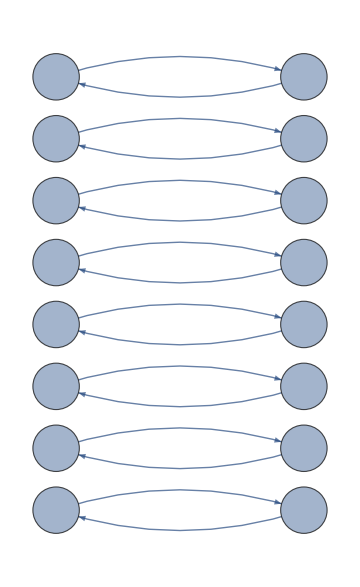

PDF[DiscreteMarkovProcess[{1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16},SparseArray[…]][∞],{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.}]

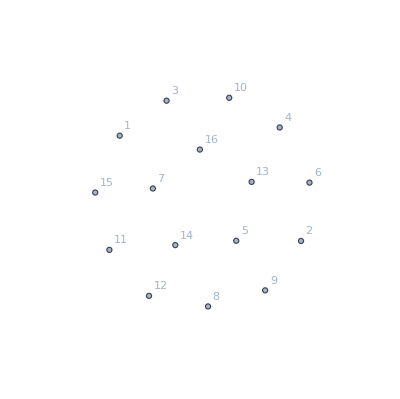

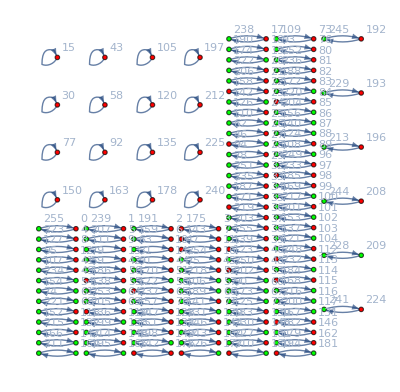

```mathematica
counter[i_,t_,r_,p_,s_,d_]:=
Module[{input = i},
assumptions = {
               If[input[[1]]==0, Q2000>Q2001, Q2000<Q2001],
               If[input[[2]]==0, Q2010>Q2011, Q2010<Q2011],
               If[input[[3]]==0, Q2100>Q2101, Q2100<Q2101],
               If[input[[4]]==0, Q2110>Q2111, Q2110<Q2111]
};
Assuming[assumptions,
{
q1=Simplify[Boole[Q2000>Q2001](p+d*Max[Q1000,Q1001])+Boole[Q2000<Q2001](t+d*Max[Q1010,Q1011])],q2=Simplify[Boole[Q2000>Q2001](s+d*Max[Q1100,Q1101])+Boole[Q2000<Q2001](r+d*Max[Q1110,Q1111])],q3=Simplify[Boole[Q2100>Q2101](p+d*Max[Q1000,Q1001])+Boole[Q2100<Q2101](t+d*Max[Q1010,Q1011])],q4=Simplify[Boole[Q2100>Q2101](s+d*Max[Q1100,Q1101])+Boole[Q2100<Q2101](r+d*Max[Q1110,Q1111])],q5=Simplify[Boole[Q2010>Q2011](p+d*Max[Q1000,Q1001])+Boole[Q2010<Q2011](t+d*Max[Q1010,Q1011])],q6=Simplify[Boole[Q2010>Q2011](s+d*Max[Q1100,Q1101])+Boole[Q2010<Q2011](r+d*Max[Q1110,Q1111])],q7=Simplify[Boole[Q2110>Q2111](p+d*Max[Q1000,Q1001])+Boole[Q2110<Q2111](t+d*Max[Q1010,Q1011])],q8=Simplify[Boole[Q2110>Q2111](s+d*Max[Q1100,Q1101])+Boole[Q2110<Q2111](r+d*Max[Q1110,Q1111])]
}];

sol=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111},
                        {Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111}];
output = {0,0,0,0};
output[[1]]=Boole[sol[[1]][[1]][[2]] < sol[[1]][[2]][[2]]];
output[[2]]=Boole[sol[[1]][[3]][[2]] < sol[[1]][[4]][[2]]];
output[[3]]=Boole[sol[[1]][[5]][[2]] < sol[[1]][[6]][[2]]];
output[[4]]=Boole[sol[[1]][[7]][[2]] < sol[[1]][[8]][[2]]];
output
];

(*All 16 strategies*)
strats = {};
Do[AppendTo[strats, Join[ConstantArray[0,4-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,15}];

(*Calculate the best responses*)
(*Change the values here*)
bestresps = {};
Do[AppendTo[bestresps, counter[strats[[i]],4,3,1,2,0/10]],{i,1,16}]

(*All 256 strategy pairs*)
inputlist = {};
Do[AppendTo[inputlist, Join[ConstantArray[0,8-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,255}];

(*Find the best responses to the pairs*)
counterstrats = {};
Do[
p1 =FromDigits[inputlist[[i]][[1;;4]],2] + 1 ;
p2 = FromDigits[inputlist[[i]][[5;;8]],2] + 1 ;
AppendTo[counterstrats,Join[bestresps[[p2]],bestresps[[p1]]]];
,{i,1,256}];


(*Make the small graph*)
edges = {};
Do[AppendTo[edges, FromDigits[strats[[i]],2]->FromDigits[bestresps[[i]],2]],{i,1,16}];
Graph[edges, VertexLabels->Placed[Automatic,Center],VertexSize->.75, ImageSize->Medium]

transitionmatrix = AdjacencyMatrix[edges];
P = DiscreteMarkovProcess[ConstantArray[1/16,16],transitionmatrix];
N[PDF[StationaryDistribution[P],Table[i,{i,1,16}]]]

edges = {};
Do[Do[AppendTo[edges,i->j],{j,1,16}],{i,1,16}];
weights = ConstantArray[0,Length[edges]];
Do[Do[If[i==(FromDigits[inputlist[[i]],2] )&& j==(FromDigits[bestresps[[i]],2]),weights[[(i-1)*16+j]]=1,weights[[(i-1)*16+j]]=0],{j,1,16}],{i,1,16}]
Graph[edges,VertexLabels->Automatic,EdgeStyle->Thread[edges->(Opacity[#]&/@weights)],ImageSize->Full]


(*Make the large graph*)
edges = {};
Do[AppendTo[edges, FromDigits[inputlist[[i]],2]->FromDigits[counterstrats[[i]],2]],{i,1,256}]
GraphPlot[edges, VertexLabels->Automatic, DirectedEdges->True, ImageSize->Full,VertexStyle->coloring]
```

```mathematica
FindInstance[0<d<1&&r>t>p>s&&r+s<=p+t&&(r-t)/(r-p)<=(p-s)/(r-p),{d,p,r,s,t}]
```

{{d→1/2,p→0,r→1,s→-1,t→1/2}}